#### Antisymmetric real random matrix

```mathematica
directory=SetDirectory[NotebookDirectory[]]
Needs["PacletManager`"]
PacletInstall[directory<>"/MaTeX-1.7.8.paclet"]
<<MaTeX`
```

```mathematica
(* size of the random matrix *)
```

```mathematica
n=10000;
(* standard deviation *)
J=1;
σ=J/(√n);
m=J0/n;
J0=8;
energies={};
```

```mathematica
samples=1;
```

```mathematica
For[ns=1,ns<=samples,ns++,
(* Generate symmetric real random matrix H *)
Hij=Table[If[i<j,RandomVariate[NormalDistribution[m,σ],1][[1]],0],{i,1,n},{j,1,n}];
H=ⅈ*(Hij-Transpose[Hij]);
(* Find and sort energy levels *)
energies=Join[energies,Sort[ Eigenvalues[H]]]];
```

```mathematica
λconst[k_]:=m*Tan[(π + 2 π k)/(2*n)];
```

```mathematica
λconst[n/2-1]//N
```

5.09296

```mathematica
λconst[n/2-2]//N
```

1.69765

```mathematica
λconst[n/2-1]+J^2/λconst[n/2-1]//N
```

5.28931

```mathematica
λconst[n/2-2]+J^2/λconst[n/2-2]//N
```

2.2867

```mathematica
energies
```

{-2.94958,-1.9979,-1.99052,-1.98752,-1.98498,-1.98409,-1.9823,-1.98062,-1.97739,-1.97675,-1.97428,9978,1.97428,1.97675,1.97739,1.98062,1.9823,1.98409,1.98498,1.98752,1.99052,1.9979,2.94958}
 |  |  |  |

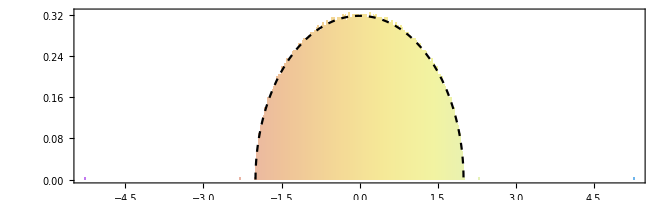

```mathematica
Plot1=Show[Histogram[energies,400,"PDF",ChartStyle->"Pastel",Frame->True,AspectRatio->0.3,FrameStyle->Directive[Black,12],FrameLabel->{{MaTeX["\\rho(\lambda)",Magnification->1.5],None},{MaTeX["\\text{$\lambda$}",Magnification->1.5],MaTeX["\\text{$N=10000$, $J = 1$, $J_{0}=8$}",Magnification->1.3]}}, PlotRange->All],Plot[1/(2π J^2)√(4 J^2-λ^2),{λ,-2J,2J},PlotStyle->{Black,Dashed}]]
```

```mathematica
Export["Plot3.pdf",Plot1]
```

Plot3.pdf